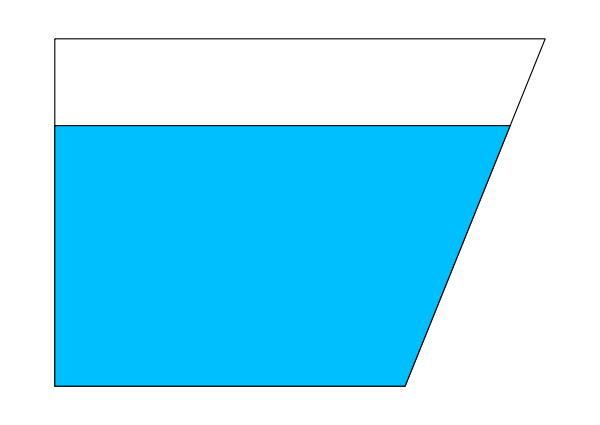

```mathematica
Module[{θ1,θ2,w1,w2,h1,h2},
θ1=60°;θ2=30°;
w1=5;w2=7;
h1=6*Sin[θ1];h2=8*Sin[θ1];

Graphics[{EdgeForm@Thick,Thick,
{FaceForm@None,Polygon[{{0,h2},{0,0},{w1,0},{w2,h2}}]},
{FaceForm@RGBColor[0,0.75,1],Polygon[{{0,h1},{0,0},{w1,0},{w1+3*Sin[θ2],h1}}]},

},ImageSize->{600,425}]
]
```